## Recovering figures from the main text figure Transient dynamics of multi-state memory

### Running the model for three cycles, each lasting for 100 time-steps.

```mathematica
newscheme={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.915, 0.3325, 0.2125]};
```

```mathematica
ClearAll;
graphs={};
onlyfrequencies={};
Table[{
initialfrequencies=Join[{45},ConstantArray[0,imax-1]];
b=1;
d=0.98;
ϵ=leach;
tmax=100;
(*dilution=5;*)
biglist={};
maxcycles=3;
initfinalpopsizes={};
For[cycle=1,cycle≤maxcycles,cycle++,
μ=0.2;
offequation=(b-d)Subscript[x, 0][t]-μ Subscript[x, 0][t]+ϵ Subscript[x, imax-1][t];
fullonequation=(b-d)Subscript[x, 1][t]-ϵ Subscript[x, 1][t]+μ Subscript[x, 0][t];
generalform[i_]:=(b-d)Subscript[x, i][t]-ϵ Subscript[x, i][t]+ϵ Subscript[x, i-1][t];
lhs=Table[Subscript[x, i]'[t],{i,0,imax-1}];
rhs=If[imax==2,Flatten[{offequation,fullonequation}],Flatten[{offequation,fullonequation,Table[generalform[i],{i,2,imax-1}]}]];
(*timelist={};*)
sol[μ_]:=NDSolve[Join[Table[lhs⟦i⟧==rhs⟦i⟧,{i,1,imax}],Table[Subscript[x, i][0]==initialfrequencies⟦i+1⟧,{i,0,imax-1}]],Table[Subscript[x, i],{i,0,imax-1}],{t,0,tmax},PrecisionGoal->Automatic];
toappend=Flatten[Table[Evaluate[Table[Subscript[x, i][t],{i,0,imax-1}]/.sol[μ]],{t,0,tmax}],1];
AppendTo[initfinalpopsizes,{toappend⟦1⟧//Total,toappend⟦-2⟧//Total}];
initialfrequencies=toappend⟦-1⟧;
AppendTo[biglist,Drop[toappend,-1]];
];
flatlist=Flatten[biglist,1];
frequencies=#/Total[#]&/@flatlist;
offlist=frequencies⟦All,1⟧;
onlist=Table[∑_(i=2)^imax frequencies⟦j,i⟧,{j,1,Length[frequencies]}];
AppendTo[onlyfrequencies,onlist];
AppendTo[graphs,{GeometricMean[Table[1/(tmax -1)(Log[initfinalpopsizes⟦i,2⟧]-Log[initfinalpopsizes⟦i,1⟧]),{i,1,maxcycles,1}]],(Log[flatlist⟦-1⟧//Total]-Log[flatlist⟦1⟧//Total])/(maxcycles tmax -1)//N,ListLogPlot[Table[flatlist⟦All,i⟧,{i,1,imax}],Joined->True,PlotStyle->Flatten[{newscheme⟦1⟧,Lighter[newscheme⟦15⟧,#]&/@Table[1-1/(imax-1) i,{i,1,imax-1}]}],DataRange->{0,tmax maxcycles},PlotRange->{{0,60},{0.01,200}},GridLines->{Table[tmax cycle+1,{cycle,1,maxcycles}], None},(*PlotLegends->Table[i,{i,0,imax-1}],*)Frame->True,FrameStyle->Directive[Black,Thickness[0.004]]],ListPlot[Table[frequencies⟦All,i⟧,{i,1,imax}],Joined->True,PlotStyle->Flatten[{newscheme⟦1⟧,Lighter[newscheme⟦15⟧,#]&/@Table[1-1/(imax-1) i,{i,1,imax-1}]}],DataRange->{0,tmax maxcycles},PlotRange->{{0,60},{-0.1,1.1}},GridLines->{Table[tmax cycle+1,{cycle,1,maxcycles}], None},PlotLegends->Table[i,{i,0,imax-1}],Frame->True],
ListPlot[{offlist,onlist(*,onlist PeakDetect[onlist,0,0,0.001+Last[onlist]]*)},Joined->{True, True, False},Filling->{3->0},FillingStyle->Opacity[1],PlotStyle->Append[newscheme⟦{1,-1}⟧,Black],PlotRange->{{0,60},{-0.05,1.05}},DataRange->{0,tmax maxcycles},GridLines->{Table[tmax cycle+1,{cycle,1,maxcycles}]},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]]],Last[flatlist],Last[flatlist]//Total}]},{imax,{6,16,26,36}},{leach,{0.25,0.75,1.25,1.75}}];
```

The plots below show the population size in the on and off compartments for different leaching rates (rows) and different memory sizes (5,15,25,35). This corresponds to the main text figure Transient dynamics in multi-state memory (b).  For capturing the dynamics in (a), change the imax list above to {2,8,32}.

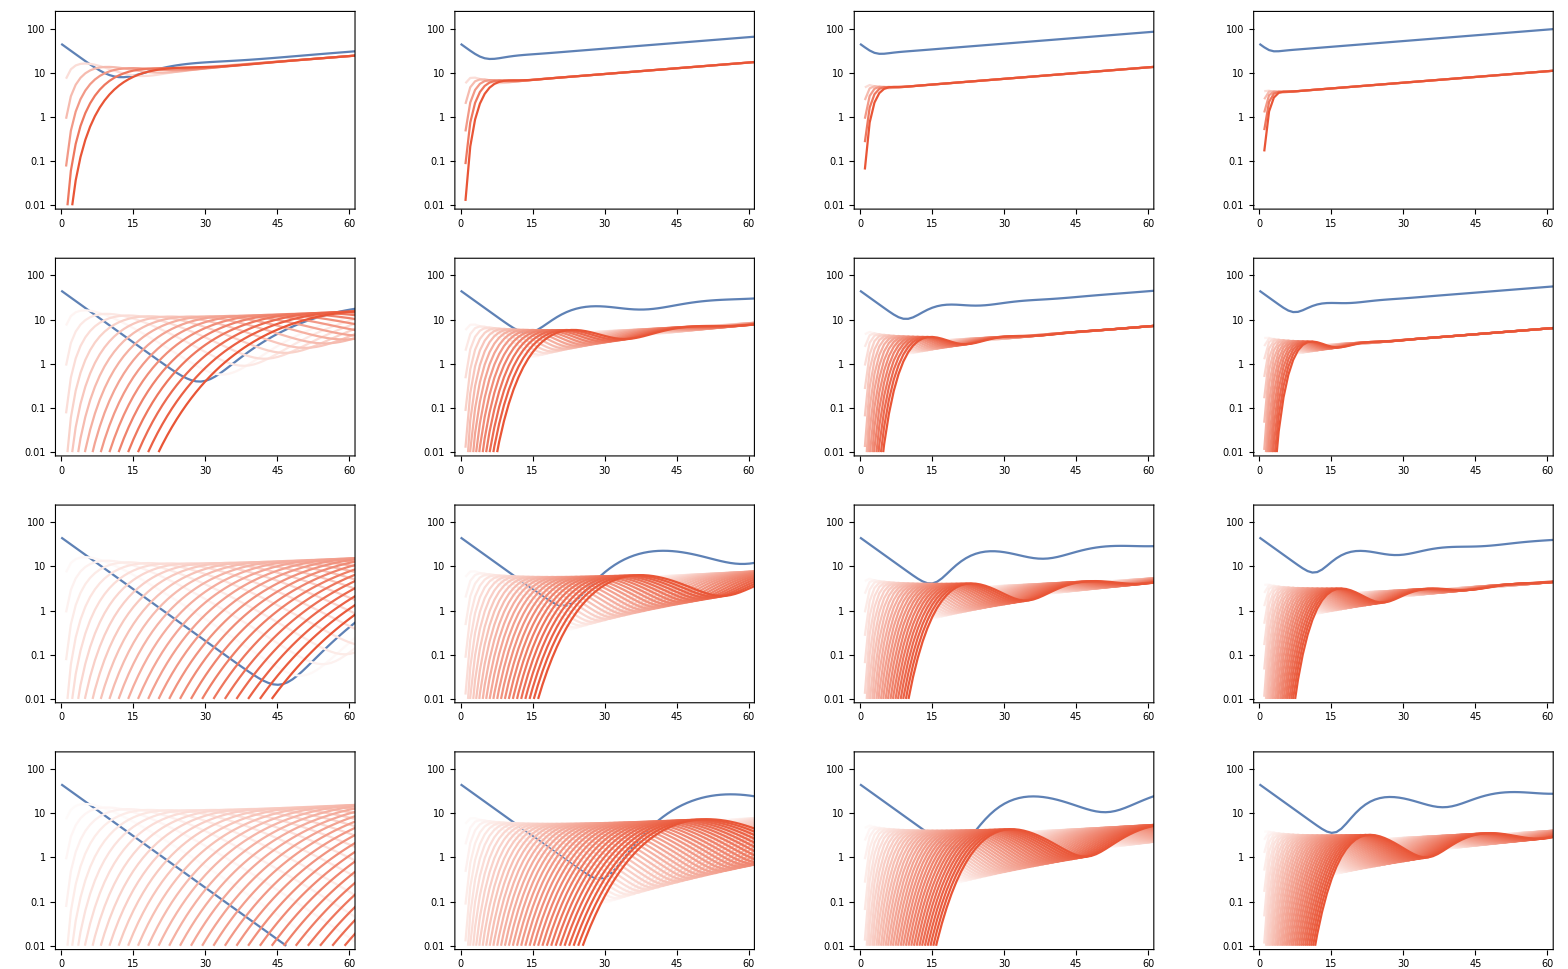

```mathematica
GraphicsGrid[Partition[graphs⟦All,3⟧,4]]
```

### Recovers the figure used in the SI eigenvalues and population dynamics

```mathematica
sublists=Partition[onlyfrequencies,4];
leachs={0.25,0.75,1.25,1.75};
place={{{50,0.5},{100,0.25},{200,0.2},{250,0.11}},{{50,0.9},{100,0.68},{200,0.53},{250,0.42}},{{250,0.95},{150,0.9},{200,0.8},{250,0.7}},{{250,0.95},{150,0.9},{200,0.8},{250,0.7}}};
```

```mathematica
Manipulate[ListPlot[Table[Callout[sublists⟦j⟧⟦i⟧,"ϵ = "<>ToString[leachs⟦i⟧],place⟦j⟧⟦i⟧,LabelStyle->Directive[14,Black],CalloutStyle->Black],{i,1,4,1}],Joined->True,PlotStyle->newscheme,(*PlotStyle->newscheme⟦4⟧,*)PlotRange->{{-10,310},{-0.05,1.05}},DataRange->{0,tmax maxcycles},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time",14,Black],Style["Frequency of on cells",14,Black]},ImagePadding->All],{j,1,Length[sublists],1}]
```

### Recovers the figure used in Main text: Transient dynamics of multi-state memory.

Focus on only the first cycle which runs for 100 time steps.

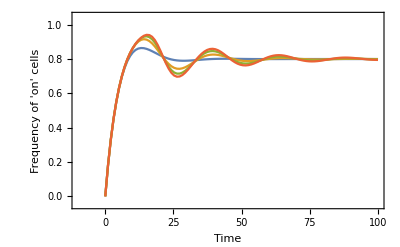

```mathematica
ListPlot[onlyfrequencies⟦{1,6,11,16},1;;100⟧,Joined->True,(*PlotStyle->newscheme⟦4⟧,*)PlotRange->{{-10,100},{-0.05,1.05}},DataRange->{0,tmax},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time",14,Black],Style["Frequency of 'on' cells",14,Black]}]
```

### Recovers the figure used in Main text: Transient dynamics of multi-state memory.

Running a quick redo of the first 100 steps now looking for the peaks and troughs

```mathematica
ClearAll;
imax=.;
bigp2p={};
popsizes={};
Table[
p2p={};
onlyfrequencies={};
Table[{
initialfrequencies=Join[{45},ConstantArray[0,imax-1]];
b=1;
d=0.98;
ϵ=leach;
tmax=100;
(*dilution=5;*)
biglist={};
maxcycles=1;
initfinalpopsizes={};
For[cycle=1,cycle≤maxcycles,cycle++,
μ=0.2;
tmax=1000;
offequation=(b-d)Subscript[x, 0][t]-μ Subscript[x, 0][t]+ϵ Subscript[x, imax-1][t];
fullonequation=(b-d)Subscript[x, 1][t]-ϵ Subscript[x, 1][t]+μ Subscript[x, 0][t];
generalform[i_]:=(b-d)Subscript[x, i][t]-ϵ Subscript[x, i][t]+ϵ Subscript[x, i-1][t];
lhs=Table[Subscript[x, i]'[t],{i,0,imax-1}];
rhs=If[imax==2,Flatten[{offequation,fullonequation}],Flatten[{offequation,fullonequation,Table[generalform[i],{i,2,imax-1}]}]];
(*timelist={};*)
sol[μ_]:=NDSolve[Join[Table[lhs⟦i⟧==rhs⟦i⟧,{i,1,imax}],Table[Subscript[x, i][0]==initialfrequencies⟦i+1⟧,{i,0,imax-1}]],Table[Subscript[x, i],{i,0,imax-1}],{t,0,tmax},PrecisionGoal->Automatic];
toappend=Flatten[Table[Evaluate[Table[Subscript[x, i][t],{i,0,imax-1}]/.sol[μ]],{t,0,tmax}],1];
AppendTo[initfinalpopsizes,{toappend⟦1⟧//Total,toappend⟦-2⟧//Total}];
initialfrequencies=toappend⟦-1⟧;
AppendTo[biglist,Drop[toappend,-1]];
];
flatlist=Flatten[biglist,1];
frequencies=#/Total[#]&/@flatlist;
offlist=frequencies⟦All,1⟧;
onlist=Table[∑_(i=2)^imax frequencies⟦j,i⟧,{j,1,Length[frequencies]}];
AppendTo[onlyfrequencies,onlist];},{imax,2,40,1}];
Table[peak=FindPeaks[onlyfrequencies⟦i⟧]⟦1⟧;
trough=Map[({x,y}=#;{x,-y})&,FindPeaks[-onlyfrequencies⟦i⟧]]⟦2⟧;
AppendTo[p2p,{(i μ)/(ϵ+i μ) ,peak⟦2⟧,trough⟦2⟧}];,{i,1,Length[onlyfrequencies]}];
AppendTo[bigp2p,Table[{p2p⟦i,1⟧,p2p⟦i,2⟧-p2p⟦i,3⟧},{i,1,Length[p2p]}]];
,{leach,{0.25,0.75,1.25,1.75}}]
```

{Null,Null,Null,Null}

#### Plotting

```mathematica
compartments=Range[2,40,1];
ListPlot[{Table[Callout[bigp2p⟦1⟧⟦i⟧,Style[compartments⟦i⟧,GrayLevel[0.7]]],{i,1,Length[bigp2p⟦1⟧]}],
Table[Callout[bigp2p⟦2⟧⟦i⟧,Style[compartments⟦i⟧,GrayLevel[0.7]]],{i,1,Length[bigp2p⟦2⟧]}],
Table[Callout[bigp2p⟦3⟧⟦i⟧,Style[compartments⟦i⟧,GrayLevel[0.7]]],{i,1,Length[bigp2p⟦3⟧]}],
Table[Callout[bigp2p⟦4⟧⟦i⟧,Style[compartments⟦i⟧,GrayLevel[0.7]]],{i,1,Length[bigp2p⟦4⟧]}]},Joined->True,Mesh->All,PlotRange->{{-0.01,1.01},{-0.01,0.3}},Frame->True,AspectRatio->1,FrameStyle->Thickness[0.003],FrameLabel->{Style["Equilibrium frequency of 'on' cells",14,Black],Style["Peak-to-peak amplitude",14,Black]},GridLines->{{0.8}, None},GridLinesStyle->Black,Epilog->Inset[Style["Switch rate μ ="<>ToString[0.2],12],{0.2,0.28}]]
```

-Graphics-